Based on Laura’s notebook

```mathematica
Quit[];
```

### Plots Styles

```mathematica
colours={ColorData[10,6],ColorData[10,1],ColorData[10,5],ColorData[10,3],ColorData[10,8],ColorData[10,2],ColorData[10,7],ColorData[10,4],ColorData[10,9]}
```

{RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275]}

```mathematica
basicdisp={AxesStyle->Directive[Black,12],LabelStyle->Directive[Black,12]};
```

### Intro, always run

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/coscattering/Laura/Xsections

```mathematica
Limp[m1_,m2_,m3_,m4_]:=Module[{E1cmt, E3cmt, E2cmt,p1cmt,p3cmt,p2cmt,tpt,tmt,p1dcmt},
E1cmt=(s+m1^2-m2^2)/(2Sqrt[s]);
p1cmt=Sqrt[E1cmt^2-m1^2];
E2cmt=(s+m2^2-m1^2)/(2Sqrt[s]);
p2cmt=Sqrt[E2cmt^2-m2^2];
E3cmt=(s+m3^2-m4^2)/(2Sqrt[s]);
p3cmt=Sqrt[E3cmt^2-m3^2];
tmt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt-p3cmt)^2;
tpt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt+p3cmt)^2;
{tpt,tmt,p1cmt,p2cmt}
]
```

```mathematica
Gammu=10^(-18) (*width of muon in GeV*)
num=.
num0={mph->1000,mX->10,mH->150,mmu->0.105,pref->1,lam->1,mwidth->Gammu*mmu}
num=Join[num0,{s->(mmu+mph)^2*del,del->10.}]
numX=Join[num0,{s->(mmu+mph)^2*del,del->XX}]
```

1/1000000000000000000

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→10.}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→XX}

```mathematica
assum={mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&Element[{mx,MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,test,nv,x,Ex,Eb,T}, Reals]}
```

{mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&(mx|MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|test|nv|x|Ex|Eb|T)∈ℝ}

```mathematica
params={MZp->20.,MD1->1.,MD2->1.02,epsilon->1.*^-6,aXM1->127.89999999999999,swsq->0.225,aEWM1->127.89999999999999,MZ->91.188,ttheta->0.00001,ME->0.0005110000000000001,cw->pow[1-swsq,0.5],sw->pow[swsq,0.5],aEW->pow[aEWM1,-1],EE->2 pow[aEW,0.5] pow[π,0.5],aX->pow[aXM1,-1],gX->2 pow[aX,0.5] pow[π,0.5],chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-0.5],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-0.5],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),0.5],DZ->0.5 pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-0.5 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],0.5]),ca->pow[1+pow[ta,2],-0.5],sa->ta pow[1+pow[ta,2],-0.5],ctheta->pow[1+pow[ttheta,2],-0.5],stheta->ttheta pow[1+pow[ttheta,2],-0.5]}/.pow->Power;
paramsnoMD2=Drop[params,{3}];
```

```mathematica
GeVm2toPb=0.389379 10^9
```

3.89379×10^8

```mathematica
(* to use Izaguare notations*)
reply={alphX->y/eps^2*MZp^4/MD1^4};
(* to use sa in the small epsilon limit*)
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
```

```mathematica
(*not used
replta={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-1/2],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),1/2],DZ->1/2pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
repltanoDZ={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],StaAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
*)
```

## Getting cross - section chi1 e-> chi2 e Zp (test=(m2-m1)/m1, vrel=test x nv) BEST OPTION

### getting M^2

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME,T}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME|T)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* Amplitude squared in eps->0 limit, propto eps^2*)
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlim=SeriesCoefficient[%,2]*eps^2
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/((-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
Msqlimc1c2=Msqlim/.MD2->MD1//Simplify
Msqlimc1c1
Msqlimc1c2/Msqlimc1c1
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

Msqlimc1c1

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/(Msqlimc1c1 (-2 MD1^2+MZp^2+s+t)^2)

### getting xsections and testing limit MD2->MD1 analytics ok

```mathematica
(* cross-section*)
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
sv=sig0*(IntMp-IntMm);
```

```mathematica
(* cross-section eps->0 limit, propto eps^2*)
IntM=Integrate[Msqlim,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMp-IntMm);
```

```mathematica
(IntMp-IntMm)
```

2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2+MD2^2)^2)/(4 s)-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2+(2 MD1 MD2 MZp^2+MZp^4+MD1^2 (2 MD2^2-MZp^2-2 s)+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s))/(MD1^2+MD2^2-MZp^2-((MD1^2+MD2^2)^2)/(4 s)-s+(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2)+(MD1^2-2 MD1 MD2+MD2^2-2 (MZp^2+s)) Log[-MD1^2-MD2^2+MZp^2+((MD1^2+MD2^2)^2)/(4 s)+s-(-1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2])-2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2+MD2^2)^2)/(4 s)-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2+(2 MD1 MD2 MZp^2+MZp^4+MD1^2 (2 MD2^2-MZp^2-2 s)+2 MZp^2 s+2 s^2-MD2^2 (MZp^2+2 s))/(MD1^2+MD2^2-MZp^2-((MD1^2+MD2^2)^2)/(4 s)-s+(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2)+(MD1^2-2 MD1 MD2+MD2^2-2 (MZp^2+s)) Log[-MD1^2-MD2^2+MZp^2+((MD1^2+MD2^2)^2)/(4 s)+s-(1/2 √(((-MD2^2+s)^2)/s)+√(-MD1^2+((MD1^2+s)^2)/(4 s)))^2])

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
svlimc1c2=svlim/.MD2->MD1//Simplify
svlimc1c1
Rsv=svlimc1c2/svlimc1c1
```

(ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2)

svlimc1c1

(ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2 svlimc1c1)

```mathematica
(*Weird, when I first give all params except M2 and then M2 it gives a different numerical result...*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params;
tmt=tm/.ss[[2,1]]//.params;
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.paramsnoMD2/.params
(*test0*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
test*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.vrel->4*ptest/MD1//.params*)
```

{{s→0.935511},{s→1.06893}}

6.75237×10^-26

6.8679×10^-26

6.54179×10^-26

6.8679×10^-26

```mathematica
myvrel=4*ptest/MD1//.params
mys=MD1^2(1+myvrel/2)//.params
```

0.133333

1.06667

```mathematica
svlimc1c1*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
svlimc1c1*Rsv*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
```

3.89379×10^8 svlimc1c1

4.15061×10^-25

### getting series of xsection in test=(MD2-MD1)/MD1=test and vrel =2 (2+test) test+test2

```mathematica
Series[svlim//.{MD2->MD1(1+test),s->MD1^2(1+vrel/2),vrel->(4+2test)test+test2},{test,0,1},{test2,0,2}]//Normal;
svseries=Simplify[%,assum]
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1,test->del/MD1,test2->vrel-(4+2test)test}//.params
```

ComplexInfinity

ReplaceRepeated::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ComplexInfinity//.params

```mathematica
Collect[svseries/.{test2-> vrel-(4+2test)test}/.vrel-> -(2 (MD1^2-s))/MD1^2/.test-> δ,s]
```

ComplexInfinity

```mathematica
svseries//.replcoann//.reply
```

ReplaceRepeated::reps: {replcoann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {reply} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ComplexInfinity//.replcoann//.reply

## Nastya’s edition

### Velocity and δ=(MD2-MD1)/MD1 expansion

#### Expanding in δ and test2=vrel-(4+2δ)δ

```mathematica
ClearAll[vrel];
```

```mathematica
σvSeries=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2),vrel->(4+2δ)δ+test2},{δ,0,1},{test2,0,2}]//Normal//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 test2^2 (1-2 δ))/(32 MZp^4 π)

```mathematica
σvSeries=
Collect[Simplify[σvSeries/.test2->vrel-(4+2δ)δ,assum],vrel]
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2 (-1+2 δ))/(32 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ (2+δ) (-1+2 δ))/(8 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ^2 (2+δ)^2 (-1+2 δ))/(8 MZp^4 π)

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]
```

-(2 (MD1^2-s))/MD1^2

```mathematica
σvSeries=Collect[Simplify[σvSeries/.vrel-> vrels,assum],s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

#### Expanding in δ and vrel (cross-check)

```mathematica
σvSeries2=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2)},{δ,0,1},{vrel,4δ+2 δ^2,2}]//Normal;
```

```mathematica
σvSeries2=Collect[Series[σvSeries2,{δ,0,1}],vrel](*same as when expanded in δ and test2*)
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

## Analytical averaged cross section, no σ expansion, mx=MD1

#### Int over s, Eb & Ex

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

Integration over s

```mathematica
Sint=Collect[ Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum]
```

-(ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (7/30 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+9/2 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+270 (2 Ex^3-Ex mx^2) T^5 Zeta[5]))/(3 MD1^2 MZp^4 π)

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
(*ExintFermions=Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum]*)
```

```mathematica
ConditionalExpression[-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5])), Re[T]>0]
```

ConditionalExpression[-(ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5])))/(30 MD1^2 MZp^4 π), Re[T]>0]

```mathematica
ExintFermions=-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5]));
```

#### Putting together <σv>

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ,nbFermions,nbBosons,nDM,IntFermions]
```

```mathematica
nDM[x_]:=gDM/(2 π^2) MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nNR[m_,x_,g_]:=g/(2 π^2) m^2 T BesselK[2,m/T]/.T-> MD1/x;
nbFermions[x_]:=3/(4 π^2) gb Zeta[3] T^3/.T-> MD1/x;
nbBosons[x_]:=1/π^2 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
nbFermionsCalc[TT_,m_]:=(4π)/(2π)^3 NIntegrate[p^2/(ⅇ^(√(p^2+m^2)/TT)+1),{p,0,∞}]
nbBoltzmannCalc[TT_,m_]:=(4π)/(2π)^3 NIntegrate[p^2/(ⅇ^(√(p^2+m^2)/TT)),{p,0,∞}]
```

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermionsCalc[TT,10]/.gb-> 1],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbBoltzmannCalc[TT,10]/.gb-> 1]},{x,100,50000},Frame->True,FrameLabel->{"x","n"},PlotLegends-> {"n_(e, Fermi)","n_(e, Boltzmann)"}]
```

NIntegrate::inumr: The integrand p^2/(1+ⅇ^((√(100+Power[«2»]))/TT)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

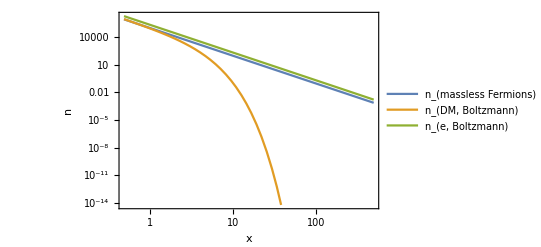

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermions[x]/.gb-> 1],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nDM[x]/.gb-> 1],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nNR[0.05,x,2]/.gb-> 1]},{x,0,500},Frame->True,FrameLabel->{"x","n"},PlotLegends-> {"n_(massless Fermions)","n_(DM, Boltzmann)","n_(e, Boltzmann)"}]
Export["densities_Fermi-DiracVsBoltmann.png",%];
```

```mathematica
nDM[0.01]
```

2.51321×10^7 gDM MD1^3

```mathematica
nbFermions[0.01]
```

2.26582×10^7 gb MD1^3

```mathematica
IntFermions[x_]:=ExintFermions/.mx-> MD1/.T-> MD1/x//FullSimplify
σvAveragedFermionsFunc[x_]:=(2 π^2)/(nDM[x] nbFermions[x])IntFermions[x]//FullSimplify
σvAveragedNR[x_]:=(m/x)/(32 π^4 nDM[x] nbFermions[x])NIntegrate[(σvSeries((s-m^2)^2)/(√s)BesselK[1,(√s x)/m])/.m-> MD1,{s,MD1^2(1+δ)^2,∞},WorkingPrecision->50]/.m-> MD1 (*non-relativistic medium frim Gondolo&Gelmini*)
```

Final result (here δ=(M2-M1)/M1)

```mathematica
σv=σvAveragedFermionsFunc[x]
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 δ) (x^3 δ (2+δ) (-7 π^4 BesselK[3,x]+45 x δ (2+δ) BesselK[2,x] Zeta[3])+2700 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(360 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

#### Plots

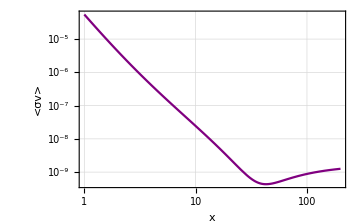

```mathematica
Show[LogLogPlot[{(*Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x],10]],*)Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x]]} ,{x,1,200},Frame->True,FrameLabel->{"x","<σv>"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple}(*,PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}*)],basicdisp,GridLines-> Automatic]
Export["Co-scattering_cross-section.png",%];
```

Cross-sections times number densities: <σ v > n_b n_x

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,x=#},N[σvAveragedNR[x],10]/σvAveragedFermionsFunc[x] ]&/@{0.001,0.01}
```

NIntegrate::precw: The precision of the argument function (((-10000+s)^2 (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.00001 √s])/(√s)) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {7.7575065902211361984621372289120625659373274374991×10^11}. NIntegrate obtained 1.4486635263897924184139294581900807894133708344434×10^34 and 6.5004703744648120965402205815241760316362802603089×10^26 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (((-10000+s)^2 (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0001 √s])/(√s)) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.0867622658906262110192747927599138410835042587823×10^10}. NIntegrate obtained 1.4486503201015447601886517260249633493989666853911×10^25 and 5.4129079177269732925206295453400268912138017638771×10^14 for the integral and error estimates.

{0.0000167186,0.0000167186}

NIntegrate::precw: The precision of the argument function (((-10000+s)^2 (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.00100014 √s])/(√s)) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {5.1548898416916604375436638541842461201278054735834×10^8}. NIntegrate obtained 1.4454932229305042650754600503736122093998645709028×10^16 and 5.0265222744752253124649012398425168466865920608931 for the integral and error estimates.

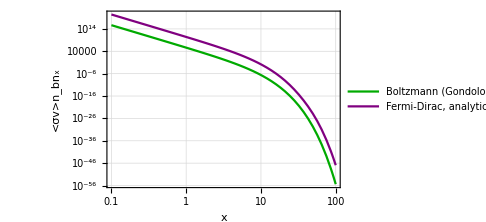

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x] nDM[x] nbFermions[x],10]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x] nDM[x] nbFermions[x]]} ,{x,0.1,100},Frame->True,FrameLabel->{"x","<σv>n_bn_x"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],basicdisp,GridLines-> Automatic]
Export["Co-scattering_cross-section-times-densities.png",%];
```

NIntegrate::precw: The precision of the argument function (((-10000+s)^2 (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0100009 √s])/(√s)) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.8645264840644084035725746841775090471607014084032×10^6}. NIntegrate obtained 1.3226070463330402352017933262511963990455231944045×10^7 and 9.6785094254841216439555541251986907126339192372587×10^-16 for the integral and error estimates.

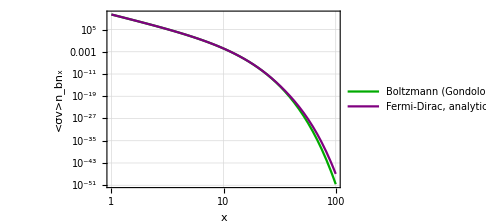

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x] nDM[x] nbFermions[x],10]/0.000016718642236630456],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x] nDM[x] nbFermions[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>n_bn_x"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],basicdisp,GridLines-> Automatic]
Export["Co-scattering_cross-section-times-densities_shifted.png",%];
```

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x] nDM[x] nbFermions[x],10]/0.000016718642236630456],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x] nDM[x] nbFermions[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>n_bn_x"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],basicdisp,GridLines-> Automatic]
```

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x] nDM[x] nbFermions[x],10]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x] nDM[x] nbFermions[x]]} ,{x,5,50},Frame->True,FrameLabel->{"x","<σv>n_bn_x"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],basicdisp,GridLines-> Automatic]
Export["Co-scattering_cross-section-times-densities_zoom-in.png",%];
```

NIntegrate::precw: The precision of the argument function (((-10000+s)^2 (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0500024 √s])/(√s)) is less than WorkingPrecision (50.).

$Aborted

#### For comparison: semi-analytical solution: Analytical integral over s, numerically over Eb and Ex

```mathematica
Sint=Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

```mathematica
σvAveragedFermionsSemiN[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Ex,MD1,∞},{Eb,0,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]
```

```mathematica
listIntSemiN=Transpose[{{1,2,5,10,20,50,100,200},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiN[#]&/@{1,2,5,10,20,50,100,200}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1,0.000054931432057976757015},{2,4.4540254397645908838×10^-6},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{200,1.2587548812224736369×10^-9}}

Compare Semi-numerical and analytical results

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[#],10]&/@{1,2,5,10,20,50,100,200}]
```

{0.0000549165,4.26924×10^-6,2.03079×10^-7,2.43544×10^-8,2.66614×10^-9,4.63094×10^-10,8.82461×10^-10,1.25875×10^-9}

```mathematica
listIntSemiN
```

{{1,0.000054931432057976757015},{2,4.4540254397645908838×10^-6},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{200,1.2587548812224736369×10^-9}}

NIntegrate::precw: The precision of the argument function ((-40000+s) √s (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0100011 √s]) is less than WorkingPrecision (50.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.8924264840644084035725746841775090471607014084032×10^6}. NIntegrate obtained 1.2668701278901150263434563805071260784300585449692×10^7 and 8.6758677911974558465205397781851905613339646830287×10^-16 for the integral and error estimates.

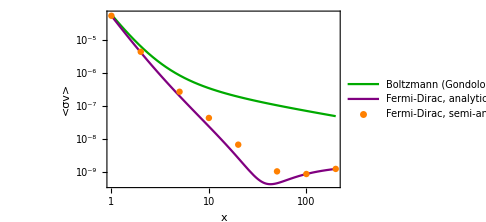

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x],10]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x]]} ,{x,1,200},Frame->True,FrameLabel->{"x","<σv>"},ImageSize->Medium,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],ListLogLogPlot[listIntSemiN,PlotStyle->Orange,PlotLegends->{"Fermi-Dirac, semi-analytically"}],basicdisp]
Export["Co-scattering_cross-section_an-semi-an.png",%];
```